```mathematica
nbPath=NotebookDirectory[];
nbDepth=FileNameDepth[nbPath];
quiccroot=FileNameJoin[FileNameSplit[nbPath][[1;;nbDepth-4]]];
dataroot=FileNameJoin[Flatten[{quiccroot,"build","Components","SparseSM","TestSuite"}]];
If[!DirectoryQ[dataroot],
Message[dataroot::wrongpath,dataroot];
Abort[];
];
$MaxExtraPrecision=1000;
(*Bessel package setup*)
pkgroot=FileNameJoin[Flatten[{quiccroot,"Components","TestSuite","Mathematica"}]];
AppendTo[$Path, pkgroot];
Bessel`$mpprec=100;
$BesselType="Insulating";
Needs["Bessel`"];
ParallelNeeds["Bessel`"]
If[$BesselType == "Value", $basis=ValueSphJnl, $basis=InsulatingSphJnl];
datadir={"_data","SparseSM","Bessel",$BesselType};
refdir={"_refdata","SparseSM","Bessel",$BesselType};
```

```mathematica
spectralExpansion[i0_,iN_,l_,g_,w_,f_,Jnl_]:=Table[Dot[w Jnl[i,l,g], f],{i,i0,iN}];
spectralDiagonal[i0_,iN_,ii_,l_,g_,w_,f_,Jnl_]:=Module[{data},
data = Table[0,{i,i0,iN}];
data[[ii+1]]=Dot[w Jnl[ii,l,g], f];
data];

(*(restricted) identity operator*)
id[row_,nN_,l_,gfunc_, wfunc_]:=Module[{s}, 
s=Table[If[row==i,1,0],{i,0,nN-1}];
s];
(* Integration opeators *)
sphlapl[row_,nN_,l_,gfunc_, wfunc_,Tnl_,Bnl_,isDiagonal_:False]:=Module[{grid,wgts,s,gN,p}, 
gN=2Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= (1/r^2 D[r^2 D[Bnl[row,l, r],r],r]-(l(l+1))/r^2 Bnl[row,l, r])//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
If[isDiagonal,
s=spectralDiagonal[0,nN-1,row,l,grid,wgts,p,Tnl];,
s=spectralExpansion[0,nN-1,l,grid,wgts,p,Tnl];
];
s];
sphlapl2[row_,nN_,l_,gfunc_, wfunc_,Tnl_,Bnl_,isDiagonal_:False]:=Module[{grid,wgts,s,gN,p}, 
gN=2Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= (1/r^2 D[r^2 D[Bnl[row,l, r],r],r]-(l(l+1))/r^2 Bnl[row,l, r])//Simplify;
s=(1/r^2 D[r^2 D[s,r],r]-(l(l+1))/r^2 s)//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
If[isDiagonal,
s=spectralDiagonal[0,nN-1,row,l,grid,wgts,p,Tnl];,
s=spectralExpansion[0,nN-1,l,grid,wgts,p,Tnl];
];
s];
(*qm[row_,nN_,l_,gfunc_, wfunc_,Tnl_,Bnl_ ,isDiagonal_:False]:=Module[{grid,wgts,s,gN,p}, 
gN=2 Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= (-D[Bnl[row,l-1, r],r]+(l-1)1/r Bnl[row,l-1, r])//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
s=spectralExpansion[0,nN-1,l,grid,wgts,p,Tnl];
s];
qp[row_,nN_,l_,gfunc_, wfunc_,Tnl_,Bnl_,isDiagonal_:False]:=Module[{grid,wgts,s,gN,p}, 
gN=2Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
s= (D[Bnl[row,l+1, r],r]+(l+2)1/r Bnl[row,l+1, r])//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
s=spectralExpansion[0,nN-1,l,grid,wgts,p,Tnl];
s];*)
qm[row_,nN_,l_,gfunc_, wfunc_,Tnl_,Bnl_ ,isDiagonal_:False]:=Module[{grid,wgts,s,gN,p,k,scale}, 
gN=2 Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];

If[SymbolName[Bnl]=="InsulatingSphJnl",
scale=bnorm[k,l-1,$insulatingDν];
k=insulatingZero[row,l-1];,
scale=bnorm[k,l-1,$valueDν];
k=valueZero[row,l-1];
];
s=k SphericalBesselJ[l,k r]/scale//Simplify;

p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
s=spectralExpansion[0,nN-1,l,grid,wgts,p,Tnl];
s];
qp[row_,nN_,l_,gfunc_, wfunc_,Tnl_,Bnl_,isDiagonal_:False]:=Module[{grid,wgts,s,gN,p,k,scale}, 
gN=2Max[nN+Floor[l/2]+3,10];
grid=gfunc[gN];
wgts=wfunc[gN];
If[SymbolName[Bnl]=="InsulatingSphJnl",
scale=bnorm[k,l+1,$insulatingDν];
k=insulatingZero[row,l+1];,
scale=bnorm[k,l+1,$valueDν];
k=valueZero[row,l+1];
];
s= k SphericalBesselJ[l,k r]/scale//Simplify;
p=s/.{r->grid};
If[Length@p < Length@grid,p=Table[p,Length@grid]];
s=spectralExpansion[0,nN-1,l,grid,wgts,p,Tnl];
s];
```

```mathematica
buildOperator[meta_,opfunc_,gfunc_,wfunc_,Tnl_,Bnl_,isDiagonal_:False]:=
Module[{outprec = 32,rows, cols,l,ref},
rows=meta[[1]];
cols=meta[[2]];
l =meta[[3]];
ref=Transpose[Table[opfunc[j,rows,l,gfunc,wfunc,Tnl,Bnl,isDiagonal],{j,0,rows-1}]];
ref=SparseArray[ref];
ref
];
```

```mathematica
(* Elementary matrix for kronecker product *)
e[i_,j_,nN_]:=Module[{mat},mat=SparseArray[{i,j}->1,{nN,nN}];mat[[i,j]]=1;mat]
(* Coefficient in front of Qp, Qm *)
coeff[l_,m_]:=(l-1)(l+1)√(((l-m)(l+m))/((2l-1)(2l+1)));
(* Inverse horizontal laplacian *)
invlaplh[l_]:=1/(l(l+1));
```

```mathematica
(* Truncation *)
m = 1;
maxL = 10;
nL=maxL-m+1;
nN=5;
```

```mathematica
(* Coriolis coupling term QP*)
Timing[
lowerQP=Table[N[coeff[l,m] invlaplh[l]buildOperator[{nN,nN,l}, qm,bgrid,bweights,ValueSphJnl,InsulatingSphJnl,False]],{l,m+1,maxL}];
upperQP=Table[N[If[l>0,-coeff[l+1,m]invlaplh[l]buildOperator[{nN,nN,l}, qp,bgrid,bweights,ValueSphJnl,InsulatingSphJnl,False],0IdentityMatrix[nN]]],{l,m,maxL-1}];
matLQP=Sum[KroneckerProduct[e[i+1,i,nL],lowerQP[[i]]],{i,1,nL-1}];
matUQP=Sum[KroneckerProduct[e[i,i+1,nL],upperQP[[i]]],{i,1,nL-1}];
matQP=matLQP+matUQP;
]
```

{46.9295,Null}

```mathematica
(* Diagonal d/dϕ T term *)
Timing[
diagonalT=Table[N[If[l>0,ⅈ m invlaplh[l] IdentityMatrix[nN],IdentityMatrix[nN]]],{l,m,maxL}];
matT = BlockDiagonalMatrix[diagonalT];
]
```

{0.006061,Null}

```mathematica
(* Coriolis coupling term QT*)
Timing[
lowerQT=Table[N[coeff[l,m]invlaplh[l]buildOperator[{nN,nN,l}, qm,bgrid,bweights,InsulatingSphJnl,ValueSphJnl,False]],{l,m+1,maxL}];
upperQT=Table[N[If[l>0,-coeff[l+1,m]invlaplh[l]buildOperator[{nN,nN,l}, qp,bgrid,bweights,InsulatingSphJnl,ValueSphJnl,False],IdentityMatrix[nN]]],{l,m,maxL-1}];
matLQT=Sum[KroneckerProduct[e[i+1,i,nL],lowerQT[[i]]],{i,1,nL-1}];
matUQT=Sum[KroneckerProduct[e[i,i+1,nL],upperQT[[i]]],{i,1,nL-1}];
matQT=matLQT+matUQT;
]
```

{11.1043,Null}

```mathematica
(* Diagonal d/dϕ∇^2 P term *)
Timing[
diagonalP=Table[N[If[l>0,ⅈ m invlaplh[l]buildOperator[{nN,nN,l}, sphlapl,bgrid,bweights,ValueSphJnl,ValueSphJnl,True],IdentityMatrix[nN]]],{l,m,maxL}];
matP=BlockDiagonalMatrix[diagonalP];
]
```

{4.20211,Null}

```mathematica
(* Toroidal mass matrix *)
Timing[
diagonalMT=Table[N[If[l>0, IdentityMatrix[nN],0IdentityMatrix[nN]]],{l,m,maxL}];
matMT = BlockDiagonalMatrix[diagonalMT];
]
```

{0.006286,Null}

```mathematica
(* Poloidal mass matrix *)
Timing[
diagonalMP=Table[N[If[l>0,buildOperator[{nN,nN,l}, sphlapl,bgrid,bweights,ValueSphJnl,ValueSphJnl,True],0IdentityMatrix[nN]]],{l,m,maxL}];
matMP=BlockDiagonalMatrix[diagonalMP];
]
```

{4.57222,Null}

```mathematica
(*Coriolis matrix and mass matrix*)
Timing[
matQ=KroneckerProduct[e[1,1,2],-matT] + KroneckerProduct[e[1,2,2],matQP] +KroneckerProduct[e[2,1,2],-matQT]+KroneckerProduct[e[2,2,2],-matP];
matM=KroneckerProduct[e[1,1,2],matMT] +KroneckerProduct[e[2,2,2],matMP];
]
```

{0.011846,Null}

{0.027721,Null}

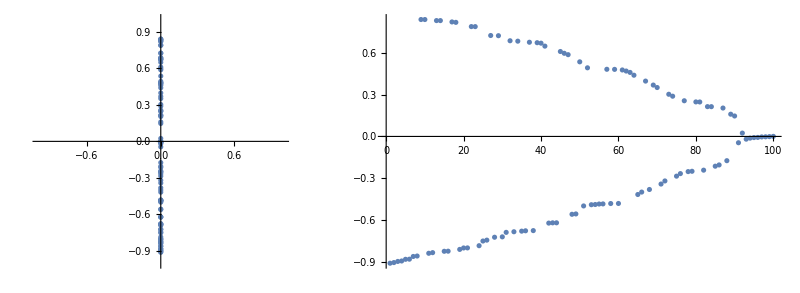

{0.-0.910356 ⅈ,7.28025×10^-17-0.905638 ⅈ,0.-0.897542 ⅈ,6.00722×10^-17-0.894334 ⅈ,7.88588×10^-17-0.882237 ⅈ,0.-0.881346 ⅈ,0.-0.861819 ⅈ,-2.01415×10^-16-0.858674 ⅈ,0.+0.83948 ⅈ,-3.043×10^-19+0.839406 ⅈ,0.-0.838948 ⅈ,5.98625×10^-17-0.834404 ⅈ,-1.07372×10^-18+0.831884 ⅈ,0.+0.831738 ⅈ,0.-0.824633 ⅈ,6.30316×10^-17-0.823951 ⅈ,0.+0.822152 ⅈ,3.57226×10^-18+0.81915 ⅈ,0.-0.811193 ⅈ,1.18838×10^-16-0.800857 ⅈ}

{-0.910356,-0.905638,-0.897542,-0.894334,-0.882237,-0.881346,-0.861819,-0.858674,-0.838948,-0.834404,-0.824633,-0.823951,-0.811193,-0.800857,-0.80037,-0.784576,-0.750923,-0.744577,-0.723725,-0.72104}

{-2.01415×10^-16,-1.98567×10^-16,-1.65354×10^-16,-1.64418×10^-16,-1.50433×10^-16,-1.11541×10^-16,-7.69714×10^-17,-5.08452×10^-17,-1.68756×10^-17,-1.42922×10^-17,-1.39095×10^-17,-4.34126×10^-18,-1.69269×10^-18,-1.07372×10^-18,-8.27582×10^-19,-3.043×10^-19,-1.2081×10^-19,-9.39758×10^-20,0.,0.}

```mathematica
(* Compute eigen spectrum *)
Timing[
ev=Eigenvalues[{Chop@matQ,Chop@matM}];
If[m==0,ev=Sort[ev][[;;-(2nN+1)]]];
]
GraphicsRow[{ComplexListPlot[ev,PlotRange->{{-1,1},{-1,1}}],ListPlot[Im@ev]}]
N[ev,5][[1;;20]]
N[Sort@Im@ev,5][[1;;20]]
N[Sort@Re@ev,5][[1;;20]]
```

```mathematica
(*N[Chop@matQP,3]//MatrixForm
N[Chop@matT,3]//MatrixForm
N[Chop@matQT,3]//MatrixForm
N[Chop@matP,3]//MatrixForm*)
```

```mathematica
(*N[Chop@matQ,3]//MatrixForm
N[Chop@matM,3]//MatrixForm*)
```